```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/julian/Projects/cs-imaging/heatmap

```mathematica
U21 = Import["U21.csv","csv"];
U23 = Import["U23.csv","csv"];
U35 = Import["U35.csv","csv"];
U41 = Import["U41.csv","csv"];
U64 = Import["U64.csv","csv"];
U51 = Import["U51.csv","csv"];
U65 = Import["U65.csv","csv"];
U75 = Import["U75.csv","csv"];
U27 = Import["U27.csv","csv"];
U26 = Import["U26.csv","csv"];
U34 = Import["U34.csv","csv"];
D12 = Import["D12.csv","csv"];
D21 = Import["D21.csv","csv"];
D23 = Import["D23.csv","csv"];
D35 = Import["D35.csv","csv"];
D41 = Import["D41.csv","csv"];
D64 = Import["D64.csv","csv"];
D51 = Import["D51.csv","csv"];
D65 = Import["D65.csv","csv"];
D75 = Import["D75.csv","csv"];
D27 = Import["D27.csv","csv"];
D26 = Import["D26.csv","csv"];
D34 = Import["D34.csv","csv"];
PathA = Import["A.csv","csv"];
PathB =  Import["B.csv","csv"];
PathC = Import["C.csv","csv"];
PathD = Import["D.csv","csv"];
PathE = Import["E.csv","csv"];;
PathF =  Import["F.csv","csv"];
```

```mathematica
nmax = Length[U21[[1]]] - 1
```

39

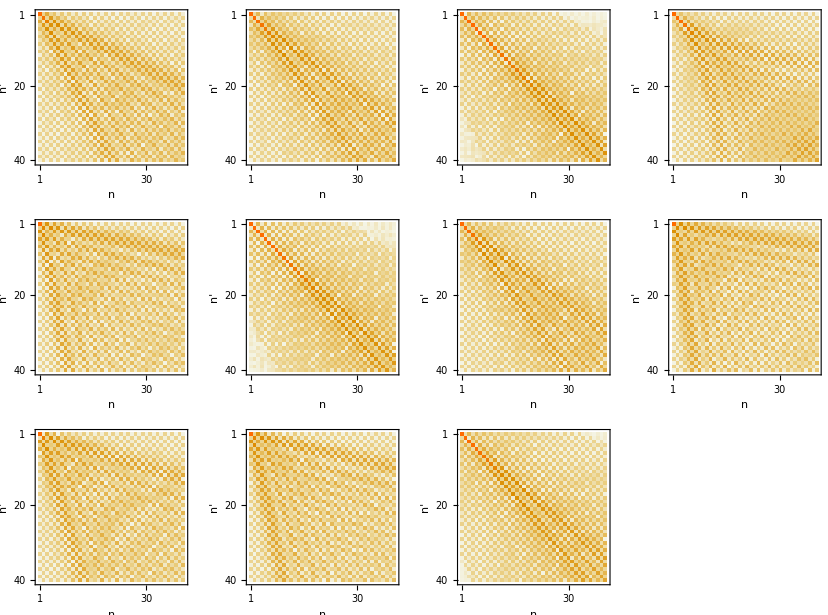

```mathematica
GraphicsGrid[{{MatrixPlot[U21,ColorFunctionScaling->True,PlotRange->{0,1},FrameLabel -> {{"n","2 -> 1"},{"n'",""}}],MatrixPlot[U23,ColorFunctionScaling->True,PlotRange->{0,1},FrameLabel -> {{"n","2 -> 3"},{"n'",""}}],MatrixPlot[U35,ColorFunctionScaling->True,PlotRange->{0,1},FrameLabel -> {{"n","3 -> 5"},{"n'",""}}],MatrixPlot[U41,ColorFunctionScaling->True,PlotRange->{0,1},FrameLabel -> {{"n","4 -> 1"},{"n'",""}}]},{MatrixPlot[U64,ColorFunctionScaling->True,PlotRange->{0,1},FrameLabel -> {{"n","6 -> 4"},{"n'",""}}],MatrixPlot[U51,ColorFunctionScaling->True,PlotRange->{0,1},FrameLabel -> {{"n","5 -> 1"},{"n'",""}}],MatrixPlot[U65,ColorFunctionScaling->True,PlotRange->{0,1},FrameLabel -> {{"n","6 -> 5"},{"n'",""}}],MatrixPlot[U75,ColorFunctionScaling->True,PlotRange->{0,1},FrameLabel -> {{"n","7 -> 5"},{"n'",""}}]},{MatrixPlot[U27,ColorFunctionScaling->True,PlotRange->{0,1},FrameLabel -> {{"n","2 -> 7"},{"n'",""}}],MatrixPlot[U26,ColorFunctionScaling->True,PlotRange->{0,1},FrameLabel -> {{"n","2 -> 6"},{"n'",""}}],MatrixPlot[U34,FrameLabel -> {{"n","3 -> 4"},{"n'",""}}]}}]
```

```mathematica
Total[U41[[6]]]
```

0.999997495581900294

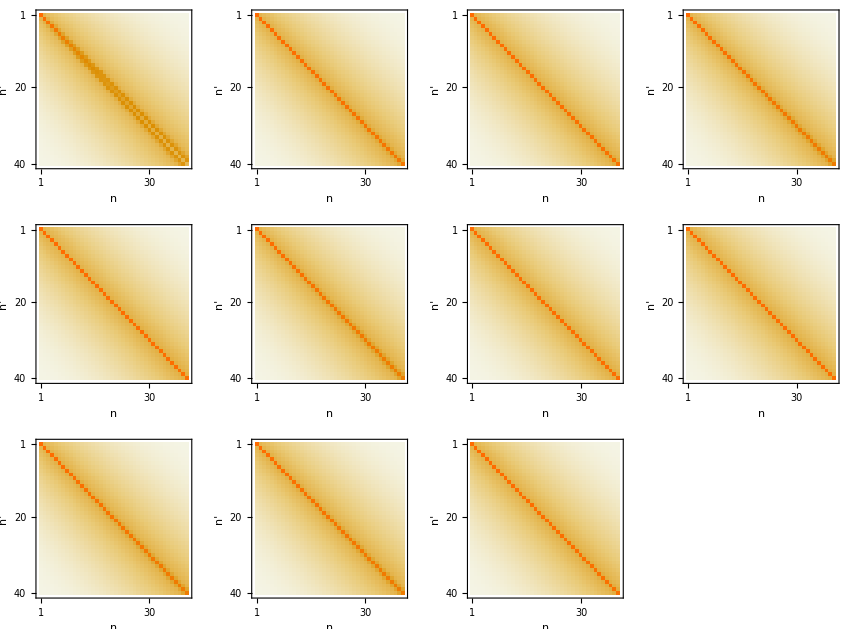

```mathematica
GraphicsGrid[{{MatrixPlot[D12,ColorFunctionScaling->True,PlotRange->{0,1},FrameLabel -> {{"n","1 -> 2"},{"n'",""}}],MatrixPlot[D23,ColorFunctionScaling->True,PlotRange->{0,1},FrameLabel -> {{"n","2 -> 3"},{"n'",""}}],MatrixPlot[D35,ColorFunctionScaling->True,PlotRange->{0,1},FrameLabel -> {{"n","3 -> 5"},{"n'",""}}],MatrixPlot[D41,ColorFunctionScaling->True,PlotRange->{0,1},FrameLabel -> {{"n","4 -> 1"},{"n'",""}}]},{MatrixPlot[D64,ColorFunctionScaling->True,PlotRange->{0,1},FrameLabel -> {{"n","6 -> 4"},{"n'",""}}],MatrixPlot[D51,ColorFunctionScaling->True,PlotRange->{0,1},FrameLabel -> {{"n","5 -> 1"},{"n'",""}}],MatrixPlot[D65,ColorFunctionScaling->True,PlotRange->{0,1},FrameLabel -> {{"n","6 -> 5"},{"n'",""}}],MatrixPlot[D75,ColorFunctionScaling->True,PlotRange->{0,1},FrameLabel -> {{"n","7 -> 5"},{"n'",""}}]},{MatrixPlot[D27,ColorFunctionScaling->True,PlotRange->{0,1},FrameLabel -> {{"n","2 -> 7"},{"n'",""}}],MatrixPlot[D26,ColorFunctionScaling->True,PlotRange->{0,1},FrameLabel -> {{"n","2 -> 6"},{"n'",""}}],MatrixPlot[D34,ColorFunctionScaling->True,PlotRange->{0,1},FrameLabel -> {{"n","3 -> 4"},{"n'",""}}]}}]
```

```mathematica
0.201004/(0.2001004+0.3678+0.25827)*3
```

0.729888

```mathematica
PathTot = 0.201004/(0.2001004+0.3678+0.25827)*PathA +0.3678/(0.2001004+0.3678+0.25827) PathB + 0.25827/(0.2001004+0.3678+0.25827) PathF;(*+ +0.001969 PathC +0.016289PathD + 0.154494PathE ;*)
Paths ={PathA, PathB, PathC, PathD, PathE, PathF, PathTot};
```

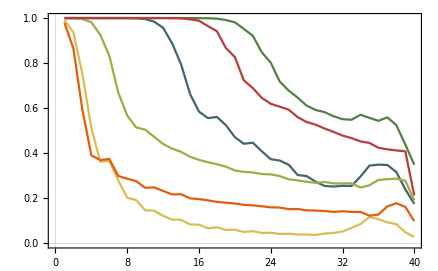

```mathematica
Show[{ListPlot[Table[Total[Table[Abs[PathA[[l,j+1]]],{j,0,nmax}]],{l,1,nmax+1}],PlotStyle -> ColorData["DarkRainbow"][1/6], Joined -> True, PlotTheme -> "Scientific",PlotRange-> All],ListPlot[Table[Total[Table[Abs[PathB[[l,j+1]]],{j,0,nmax}]],{l,1,nmax+1}],PlotStyle -> ColorData["DarkRainbow"][2/6],Joined -> True,PlotTheme -> "Scientific",PlotRange-> All],ListPlot[Table[Total[Table[Abs[PathC[[l,j+1]]],{j,0,nmax}]],{l,1,nmax+1}],PlotStyle -> ColorData["DarkRainbow"][3/6],Joined -> True,PlotTheme -> "Scientific",PlotRange-> All],ListPlot[Table[Total[Table[Abs[PathD[[l,j+1]]],{j,0,nmax}]],{l,1,nmax+1}],PlotStyle -> ColorData["DarkRainbow"][4/6],Joined -> True,PlotTheme -> "Scientific",PlotRange-> All],ListPlot[Table[Total[Table[Abs[PathE[[l,j+1]]],{j,0,nmax}]],{l,1,nmax+1}],PlotStyle -> {ColorData["DarkRainbow"]}[5/6],Joined -> True,PlotTheme -> "Scientific",PlotRange-> All],ListPlot[Table[Total[Table[Abs[PathF[[l,j+1]]],{j,0,nmax}]],{l,1,nmax+1}],PlotStyle -> {ColorData["DarkRainbow"][6/6]},Joined -> True,PlotTheme -> "Scientific",PlotRange-> All]}]
```

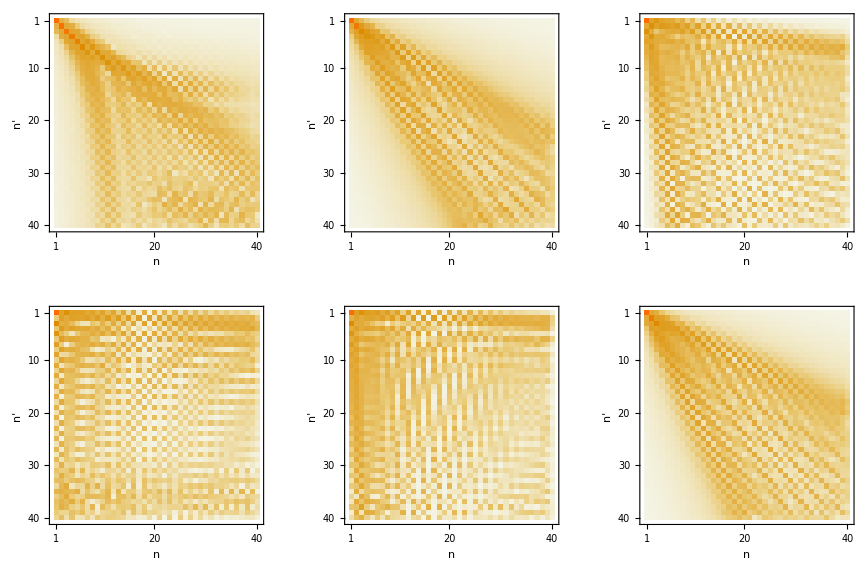

```mathematica
GraphicsGrid[{{MatrixPlot[PathA,FrameLabel -> {{"n","Path A: 2 -> 3 -> 4 -> 1"},{"n'",""}},FrameStyle-> Black,ColorFunctionScaling->True,PlotRange->{0,1} ],
MatrixPlot[PathB,FrameLabel -> {{"n","Path B: 2 -> 3 -> 5 -> 1"},{"n'",""}},FrameStyle-> Black,ColorFunctionScaling->True,PlotRange->{0,1} ],
MatrixPlot[PathC,FrameLabel -> {{"n","Path C: 2 -> 6 -> 5 -> 1"},{"n'",""}},FrameStyle-> Black ,ColorFunctionScaling->True,PlotRange->{0,1}]
},
{MatrixPlot[PathD,FrameLabel -> {{"n","Path D: 2 -> 6 -> 4 -> 1"},{"n'",""}},FrameStyle-> Black ,ColorFunctionScaling->True,PlotRange->{0,1}],
MatrixPlot[PathE,FrameLabel -> {{"n","Path E: 2 -> 7 -> 5 -> 1"},{"n'",""}},FrameStyle-> Black ,ColorFunctionScaling->True,PlotRange->{0,1}],
MatrixPlot[PathF,FrameLabel -> {{"n","Path F: 2 -> 1"},{"n'",""}},FrameStyle-> Black,ColorFunctionScaling->True,PlotRange->{0,1} ]}}, FrameStyle-> Black]
```

```mathematica
Total[PathE[[2]]]
```

0.864776814255861957

```mathematica
tablePath[pa_]:=Table[Sum[Paths[[pa]][[r,All]][[ra]] ra,{ra,1,nmax+1}],{r,1,Length[Paths[[pa]][[1,All]]]}]
tablePath[4]
```

{5.79252056207427585,13.8823565800877868,14.2894711014142562,8.78216019170851454,4.35496694270051019,6.19940850161673815,4.68074752812891288,2.66343098105943457,3.13656069198026308,1.96920161275846934,2.23856327120138826,1.85510321968299759,1.53654632181684175,1.75538209998586759,1.11662125374757021,1.28836741801720222,0.830759020447772483,1.18010626084210985,0.754637823169187737,0.906251070574274686,0.649583157967500254,0.859895651001417622,0.571754721857987801,0.688684838283170588,0.584764522266456459,0.612028601391500465,0.552386983886014989,0.581597255663082622,0.507307145153354521,0.609724857128548518,0.668094863237631121,0.72897328041211969,1.13998779120184992,1.16816949755475946,1.84287025699484554,1.63311691293996716,1.4114861541689565,1.39517041007892492,0.847373968749513094,0.381563878097979387}

```mathematica
plotPath[pa_]:=ListPlot[Table[Sum[Paths[[pa]][[r,All]][[ra]] ra,{ra,1,nmax+1}],{r,1,Length[Paths[[pa]][[1,All]]]}],PlotStyle -> ColorData["DarkRainbow"][pa/6],Joined -> True,PlotRange-> All]
Show[{Plot[x,{x,1,12}, PlotStyle -> Directive[Black, Thin], PlotTheme -> "Scientific"],Table[plotPath[p],{p,1,6}]},PlotRange-> {{1,15},{0,20}}, FrameLabel->{"n", "n'"}, FrameStyle -> Black]
```

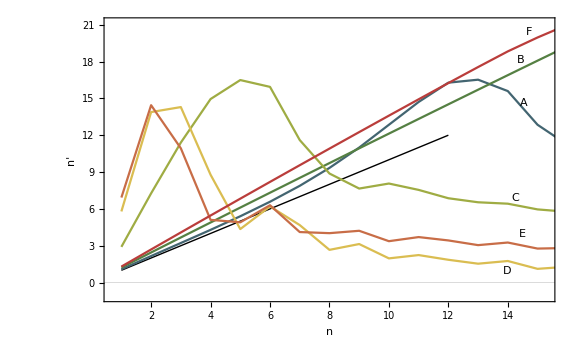

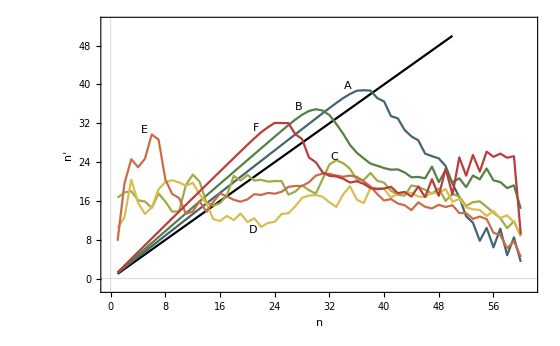

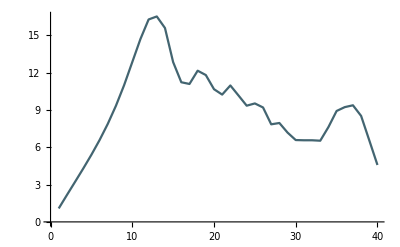
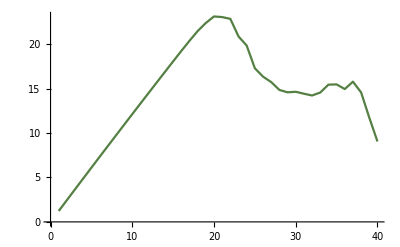
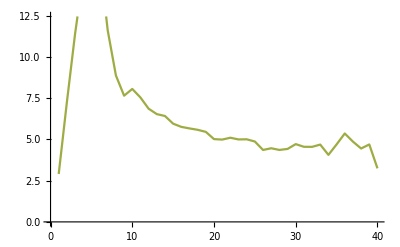
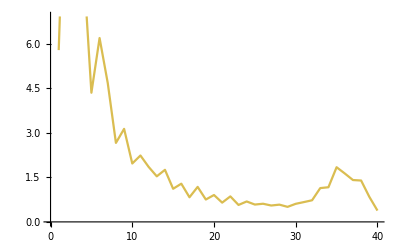
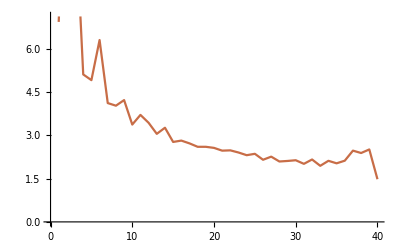
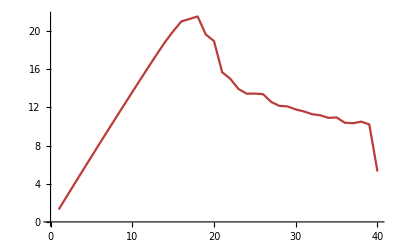

```mathematica
Table[plotPath[p],{p,1,6}]
```

```mathematica
MatrixPlot[PathTot]
```

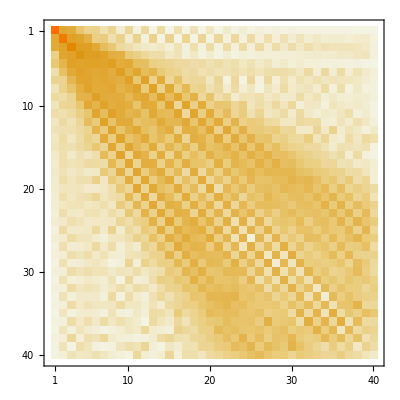
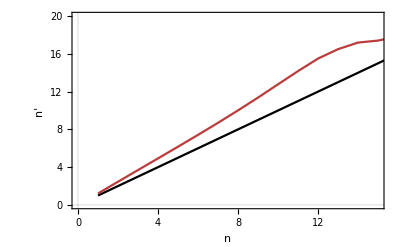

```mathematica
Show[{Plot[x,{x,1,50}, PlotStyle -> Directive[Black], PlotTheme -> "Scientific"],Table[plotPath[p],{p,7,7}]},PlotRange -> {{0,15},{0,20}}, FrameLabel->{"n", "n'"}, FrameStyle -> Black]
```

-Graphics-